-Graphics-

S = 2 πrh + 2 πr^2

Define the function.  The “N” makes sure I get a number.

```mathematica
s[r_, h_] := N[2 π r h + 2 π r^2]
```

Use the function

```mathematica
r= 5;
h = 10;
myAnswer = s[r,h]
```

471.239

Make a table of the function

```mathematica
results = Table[
{
number,
s[number,h]
},
{number,1,10}
];
Grid[Prepend[results, {"Number","Function"}], Frame -> All]
```

Number | Function
1 | 69.115
2 | 150.796
3 | 245.044
4 | 351.858
5 | 471.239
6 | 603.186
7 | 747.699
8 | 904.779
9 | 1074.42
10 | 1256.64

If you need to remove the units, you can use “/. cm^2 → 1"

Plot the function with one variable a constant.  Notice that I don’t use ANY units, so it plots!

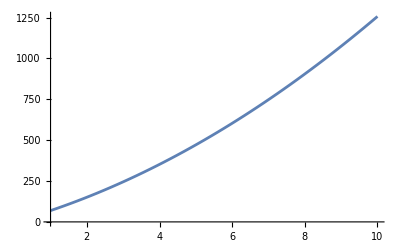

```mathematica
Plot[s[number,h],{number,1,10}]
```

Plot the function with both variables changing

```mathematica
Plot3D[s[r,h], {r,1,5}, {h,1,10}]
```

-Graphics3D-

Code and plot the logistic function

ΔP = (P_0 M)/((M - P_0) e^-rt + P_0)

```mathematica
dA[a0_, b_] :=a0/E^(-a0 b)
a0 = 10;
Plot[dA[a0,b], {b,1,10}]
```

-Graphics-